```mathematica
anzahlInput = 3; anzahlOutput = 1;
l = 5; (*Anzahl Sektoren*)
modulo[z_] := Exp[I Mod[Arg[z],2 Pi/l]];
toComplex[x_] := Exp[I 2 Pi /l x];
toReal[z_] := Arg[z] / ((2 Pi)/l);
round[z_] := z /modulo[z];
Activ[z_] := toReal[modulo[z]];
```

```mathematica
weights = Table[N[Exp[I   RandomInteger[{1,256}]/256]],{anzahlOutput},{anzahlInput}]
```

{{0.74225+0.670123 ⅈ,0.99695+0.0780456 ⅈ,0.543585+0.839354 ⅈ}}

```mathematica
in= {{0.1,0.1,0.9},{0.1,0.9,0.9},{0.9,0.1,0.9},{0.9,0.9,0.9}};
in = toComplex[in]
```

{{0.992115+0.125333 ⅈ,0.992115+0.125333 ⅈ,0.425779+0.904827 ⅈ},{0.992115+0.125333 ⅈ,0.425779+0.904827 ⅈ,0.425779+0.904827 ⅈ},{0.425779+0.904827 ⅈ,0.992115+0.125333 ⅈ,0.425779+0.904827 ⅈ},{0.425779+0.904827 ⅈ,0.425779+0.904827 ⅈ,0.425779+0.904827 ⅈ}}

```mathematica
out= {{0.1},{0.9},{0.9},{0.9}};
out = toComplex[out]
```

{{0.992115+0.125333 ⅈ},{0.425779+0.904827 ⅈ},{0.425779+0.904827 ⅈ},{0.425779+0.904827 ⅈ}}

```mathematica
(*Trainiere Perzeptron*)
```

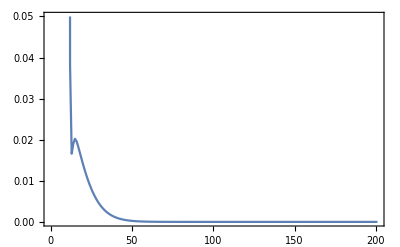

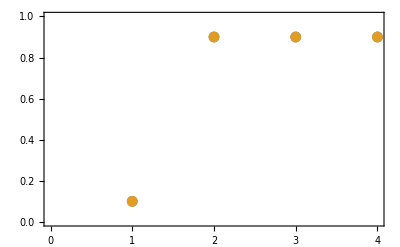

{{0.1,0.9,0.9,0.9}}

{{0.1,0.9,0.9,0.9}}

{{-5.20871×10^-8,4.70876×10^-9,1.47521×10^-7,-1.12817×10^-8}}

```mathematica
w1=Table[
(*Lerne*)
Do[
eta=1;
netin =weights.in[[i]];
soll = out[[i]] * round[netin];
error = soll -netin;
diff=Outer[Times, eta/(anzahlInput+1)*error,Conjugate[in[[i]]]];
weights += diff;
,{i,1,4}];
(*Berechne Error*)
err=Transpose[toReal[out]]-Activ[weights.Transpose[in]];
	1/2*(err.Transpose[err])[[1,1]]
,{epoche,0,200}];
ListPlot[w1,Frame->True,Joined->True,PlotRange->{0,0.05}](*Printe error*)
(*Schaue ob funktioniert*)
result=Table[Activ[weights.in[[i]]],{i,4}];
result=Transpose[result];
should=Table[toReal[out[[i]]],{i,4}];
should=Transpose[should];
ListPlot[{result[[1]],should[[1]]},Frame->True,PlotRange->{0,1}]
result
should
should-result
```

```mathematica
err=Transpose[toReal[out]]-Activ[weights.Transpose[in]];
	1/2*(err.Transpose[err])[[1,1]]
```

1.23126×10^-14